# EWPT of the VDDMM

## Loading package and Feynman rules

```mathematica
NotebookEvaluate["/home/bastilo/Dropbox/ProyectoVectorDM/ObliqueParameters/New/DefinicionesV2.nb"];
Options[OneLoop];
```

Loading FeynCalc from /home/bastilo/.Mathematica/Applications/HighEnergyPhysics

HighEnergyPhysics`FeynCalc`MemoryAvailable`MemoryAvailable::shdw: Symbol MemoryAvailable appears in multiple contexts {HighEnergyPhysics`FeynCalc`MemoryAvailable`,System`}; definitions in context HighEnergyPhysics`FeynCalc`MemoryAvailable` may shadow or be shadowed by other definitions.

FeynCalc 8.2.0 For help, type ?FeynCalc, open FeynCalcRef8.nb or visit www.feyncalc.org

Loading PHI

WARNING! Your FeynArts installation is not complete or the version you have cannot be used with this version of FeynCalc.
FeynArts can be downloaded at www.feynarts.de

Loading FeynArts, see www.feynarts.de for documentation

FeynArts not found. Please install FeynArts, e.g., in
/home/bastilo/.Mathematica
and reload FeynCalc
FeynArts can be downloaded from www.feynarts.de

```mathematica
Install["/home/bastilo/Documents/Programas/LoopTools-2.15/x86_64-Linux/bin/LoopTools"];
```

PaVe::shdw: Symbol PaVe appears in multiple contexts {LoopTools`,HighEnergyPhysics`fcloops`PaVe`}; definitions in context LoopTools` may shadow or be shadowed by other definitions.

Li2::shdw: Symbol Li2 appears in multiple contexts {LoopTools`,HighEnergyPhysics`FeynCalc`}; definitions in context LoopTools` may shadow or be shadowed by other definitions.

A0::shdw: Symbol A0 appears in multiple contexts {LoopTools`,HighEnergyPhysics`fctables`A0`}; definitions in context LoopTools` may shadow or be shadowed by other definitions.

B0::shdw: Symbol B0 appears in multiple contexts {LoopTools`,HighEnergyPhysics`fctables`B0`}; definitions in context LoopTools` may shadow or be shadowed by other definitions.

B1::shdw: Symbol B1 appears in multiple contexts {LoopTools`,HighEnergyPhysics`fctables`B1`}; definitions in context LoopTools` may shadow or be shadowed by other definitions.

B00::shdw: Symbol B00 appears in multiple contexts {LoopTools`,HighEnergyPhysics`fctables`B00`}; definitions in context LoopTools` may shadow or be shadowed by other definitions.

B11::shdw: Symbol B11 appears in multiple contexts {LoopTools`,HighEnergyPhysics`fctables`B11`}; definitions in context LoopTools` may shadow or be shadowed by other definitions.

DB0::shdw: Symbol DB0 appears in multiple contexts {LoopTools`,HighEnergyPhysics`fctables`DB0`}; definitions in context LoopTools` may shadow or be shadowed by other definitions.

DB1::shdw: Symbol DB1 appears in multiple contexts {LoopTools`,HighEnergyPhysics`fctables`DB1`}; definitions in context LoopTools` may shadow or be shadowed by other definitions.

C0::shdw: Symbol C0 appears in multiple contexts {LoopTools`,HighEnergyPhysics`fctables`C0`}; definitions in context LoopTools` may shadow or be shadowed by other definitions.

D0::shdw: Symbol D0 appears in multiple contexts {LoopTools`,HighEnergyPhysics`fctables`D0`}; definitions in context LoopTools` may shadow or be shadowed by other definitions.

====================================================
   FF 2.0, a package to evaluate one-loop integrals
 written by G. J. van Oldenborgh, NIKHEF-H, Amsterdam
 ====================================================
 for the algorithms used see preprint NIKHEF-H 89/17,
 'New Algorithms for One-loop Integrals', by G.J. van
 Oldenborgh and J.A.M. Vermaseren, published in 
 Zeitschrift fuer Physik C46(1990)425.
 ====================================================

## Vaccum polarization Amplitudes

WW-polarization

```mathematica
-Graphics- + -Graphics- +-Graphics- +-Graphics-;
```

## Amplitudes

```mathematica
MWW1=Contract[WVCV1[-q,q-l,l,μ,a,d].propVC[q-l,b,a].WVCV1[q,-q+l,-l,ν,b,s].propV1[l,s,d]];
MWW1L=OneLoop[l,%];
MWW1LPV=Simplify[PaVeReduce[MWW1L]];

MWW2=Contract[WVCV2b[-q,q-l,l,μ,a,d].propVC[q-l,b,a].WVCV2a[q,-q+l,-l,ν,b,s].propV2[l,d,s]];
MWW2L=OneLoop[l,%];
MWW2LPV=Simplify[PaVeReduce[MWW2L]];

MWW3=Contract[WWVCVC[μ,ν,α,β].propVC[q-l,α,β]];
MWW3L=OneLoop[l,%];
MWW3LPV=Simplify[PaVeReduce[MWW3L]];

MWW41=Contract[WWV1V1[μ,ν,α,β].propV1[q-l,α,β]];
MWW41L=OneLoop[l,%];
MWW41LPV=Simplify[PaVeReduce[MWW41L]];

MWW42=Contract[WWV2V2[μ,ν,α,β].propV2[q-l,α,β]];
MWW42L=OneLoop[l,%];
MWW42LPV=Simplify[PaVeReduce[MWW42L]];
```

## Sum of amplitudes

```mathematica
MWW=I/(64*π^4)Simplify[MWW1LPV+MWW2LPV+MWW3LPV+MWW41LPV+MWW42LPV];
ScalarProduct[FV[y,μ],FV[y,μ]]=1;
ScalarProduct[FV[q,μ],FV[y,μ]]=0;
ScalarProduct[y,y]=1;
ScalarProduct[q,y]=0;
```

## Getting the term proportional to gmunu

```mathematica
ΠWW=Expand[Contract[MWW,FV[y,μ].FV[y,ν]]];
ΠWWx=ΠWW/.ScalarProduct[q,q]->x;
```

## Replacing A0 to B0 and expanding B0(x,m1,m2)

```mathematica
(*SetOptions[A0,A0ToB0->True];
```

```mathematica
BB12=Normal[Series[B0[x,MV1^2,MV2^2],{x,0,1}]];
BB1C=Normal[Series[B0[x,MV1^2,MVC^2],{x,0,1}]];
BB2C=Normal[Series[B0[x,MV2^2,MVC^2],{x,0,1}]];
```

## The amplitude after replacements

```mathematica
WWF=Simplify[ΠWWx/.{B0[x,MV1^2,MV2^2]-> BB12}/.{B0[x,MV1^2,MVC^2]-> BB1C}]/.{B0[x,MV2^2,MVC^2]-> BB2C};
WW0=Expand[WWF]/.{x->0};
```

ZZ-polarization

## -Graphics-+-Graphics-+-Graphics-+-Graphics-

## Amplitudes

```mathematica
MZZ1=Contract[ZVCVC[-q,q-l,l,μ,a,d].propVC[q-l,b,a].ZVCVC[q,-l,-q+l,ν,s,b].propVC[l,s,d]];
MZZ1L=OneLoop[l,%];
MZZ1LPV=Simplify[PaVeReduce[MZZ1L]];

MZZ2=Contract[ZV1V2[-q,l,q-l,μ,d,a].propV2[q-l,b,a].ZV1V2[q,-l,-q+l,ν,s,b].propV1[l,d,s]];
MZZ2L=OneLoop[l,%];
MZZ2LPV=Simplify[PaVeReduce[MZZ2L]];

MZZ3=Contract[ZZVCVC[μ,ν,α,β].propVC[q-l,α,β]];
MZZ3L=OneLoop[l,%];
MZZ3LPV=Simplify[PaVeReduce[MZZ3L]];

MZZ41=Contract[ZZV1V1[μ,ν,α,β].propV1[q-l,α,β]];
MZZ41L=OneLoop[l,%];
MZZ41LPV=Simplify[PaVeReduce[MZZ41L]];

MZZ42=Contract[ZZV2V2[μ,ν,α,β].propV2[q-l,α,β]];
MZZ42L=OneLoop[l,%];
MZZ42LPV=Simplify[PaVeReduce[MZZ42L]];
```

## Sum of amplitudes

```mathematica
MZZ=I/(64*π^4)Simplify[MZZ1LPV+MZZ2LPV+MZZ3LPV+MZZ41LPV+MZZ42LPV];
ScalarProduct[FV[y,μ],FV[y,μ]]=1;
ScalarProduct[FV[q,μ],FV[y,μ]]=0;
ScalarProduct[y,y]=1;
ScalarProduct[q,y]=0;
```

Set::setraw: Cannot assign to raw object 1.

## Getting the term proportional to gmunu

```mathematica
ΠZZ=Expand[Contract[MZZ,FV[y,μ].FV[y,ν]]];
ΠZZx=ΠZZ/.ScalarProduct[q,q]->x;
```

## The amplitude after replacements

```mathematica
ZZF=Simplify[ΠZZx/.{B0[x,MV1^2,MV2^2]-> BB12}/.{B0[x,MV1^2,MVC^2]-> BB1C}]/.{B0[x,MV2^2,MVC^2]-> BB2C};
ZZ0=Expand[ZZF]/.{x->0};
```

```mathematica
(*SetOptions[A0,A0ToB0->False];
```

Zγ-Amplitude polarization

```mathematica
MZγ=Contract[AZVCVC[μ,ν,α,β].propVC[q-l,α,β]];
MZγL=OneLoop[l,%];
MZγLPV=Simplify[PaVeReduce[MZγL]];
```

## Getting the term proportional to gmunu

```mathematica
ΠZγ=Contract[MZγLPV,FV[y,μ].FV[y,ν]];
ΠZγx=ΠZγ/.ScalarProduct[q,q]->x;
```

## Expanding some amplitudes and replacing q^2->MZ^2

```mathematica
ZγF=Simplify[ΠZγx/.{B0[x,MV1^2,MV2^2]-> BB12}/.{B0[x,MV1^2,MVC^2]-> BB1C}]/.{B0[x,MV2^2,MVC^2]-> BB2C};
ZγMZ=Expand[ZγF]/.{x->MZ^2};
```

T-parameter (Simple form)

```mathematica
T1=(WW0/(cw*MZ)^2-ZZ0/MZ^2)/α/.{α->e^2/(4π)};
```

```mathematica
(*Pag. 70 One-Loop Romao. DB0 were calculated with Mathematica*)
Rep:={
A0[MV1^2]->(MV1^2)(Δ+1-Log[MV1^2]),
A0[MV2^2]->(MV2^2)(Δ+1-Log[MV2^2]),
A0[MVC^2]->(MVC^2)(Δ+1-Log[MVC^2]),
B0[0,MV1^2,MV2^2]->Δ+1-(MV1^2Log[MV1^2]-MV2^2Log[MV2^2])/(MV1^2-MV2^2),
B0[0,MV1^2,MVC^2]->Δ+1-(MV1^2Log[MV1^2]-MVC^2Log[MVC^2])/(MV1^2-MVC^2),
B0[0,MV2^2,MVC^2]->Δ+1-(MV2^2Log[MV2^2]-MVC^2Log[MVC^2])/(MV2^2-MVC^2),
B0[0,MV1^2,MV1^2]->Δ-Log[MV1^2],
B0[0,MV2^2,MV2^2]->Δ-Log[MV2^2],
B0[0,MVC^2,MVC^2]->Δ-Log[MVC^2],
DB0[0,MV1^2,MV2^2]->-(MV1^4-MV2^4-2 MV1^2 MV2^2 Log[MV1^2/MV2^2])/(2 (MV1^2-MV2^2)^3),
DB0[0,MV1^2,MVC^2]->-(MV1^4-MVC^4-2 MV1^2 MVC^2 Log[MV1^2/MVC^2])/(2 (MV1^2-MVC^2)^3),
DB0[0,MV2^2,MVC^2]->-(MV2^4-MVC^4-2 MV2^2 MVC^2 Log[MV2^2/MVC^2])/(2 (MV2^2-MVC^2)^3)
};
```

```mathematica
(*Pag. 70 One-Loop Romao. DB0 were calculated with Mathematica*)
Repμ:={
A0[MV1^2]->(MV1^2)(Δ+1-Log[MV1^2/μ^2]),
A0[MV2^2]->(MV2^2)(Δ+1-Log[MV2^2]/μ^2),
A0[MVC^2]->(MVC^2)(Δ+1-Log[MVC^2]/μ^2),
B0[0,MV1^2,MV2^2]->Δ+1-(MV1^2Log[MV1^2]-MV2^2Log[MV2^2])/(MV1^2-MV2^2),
B0[0,MV1^2,MVC^2]->Δ+1-(MV1^2Log[MV1^2]-MVC^2Log[MVC^2])/(MV1^2-MVC^2),
B0[0,MV2^2,MVC^2]->Δ+1-(MV2^2Log[MV2^2]-MVC^2Log[MVC^2])/(MV2^2-MVC^2),
B0[0,MV1^2,MV1^2]->Δ-Log[MV1^2/μ^2],
B0[0,MV2^2,MV2^2]->Δ-Log[MV2^2/μ^2],
B0[0,MVC^2,MVC^2]->Δ-Log[MVC^2/μ^2],
DB0[0,MV1^2,MV2^2]->-(MV1^4-MV2^4-2 MV1^2 MV2^2 Log[MV1^2/MV2^2])/(2 (MV1^2-MV2^2)^3),
DB0[0,MV1^2,MVC^2]->-(MV1^4-MVC^4-2 MV1^2 MVC^2 Log[MV1^2/MVC^2])/(2 (MV1^2-MVC^2)^3),
DB0[0,MV2^2,MVC^2]->-(MV2^4-MVC^4-2 MV2^2 MVC^2 Log[MV2^2/MVC^2])/(2 (MV2^2-MVC^2)^3)
};
```

The T parameter with Rep

```mathematica
T2=T1/.Rep//Simplify;
```

The expansion of the T parameter in Δ

```mathematica
T3a=Series[T2,{Δ,0,1}]//Simplify;
T3b=Series[T2,{Δ,0,0}]//Simplify;
NumT3b=Numerator[Normal[T3b]];
NumT3b/.{MV2->MVC}
```

0

Considering the divergence

```mathematica
T30=Normal[T2]/.{Δ->Log[Λ^2/MZ^2]};
```

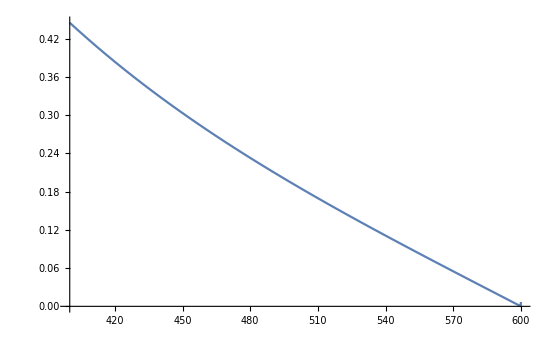

```mathematica
Block[{MV1,MV2,MVC,MZ,sw,cw,Λ},
MV2=605;
MVC=600;
sw=0.4;
cw=√(1-sw^2);
MZ=91.1;
Λ=2000;
A3=Plot[T30,{MV1,400,600}]]
```

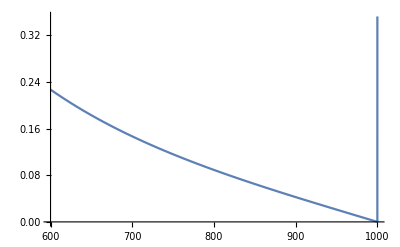

```mathematica
Block[{MV1,MV2,MVC,MZ,sw,cw,Λ},
MV2=1001;
MVC=1000;
sw=0.4;
cw=√(1-sw^2);
MZ=91.1;
Λ=2000;
A2=Plot[T30,{MV1,600,1000}]]
```

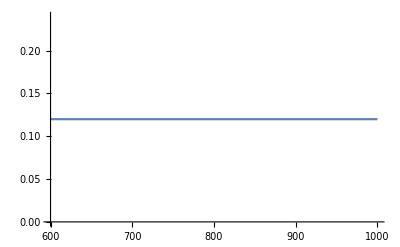

```mathematica
AR=Plot[0.12,{MV1,600,1000}]
```

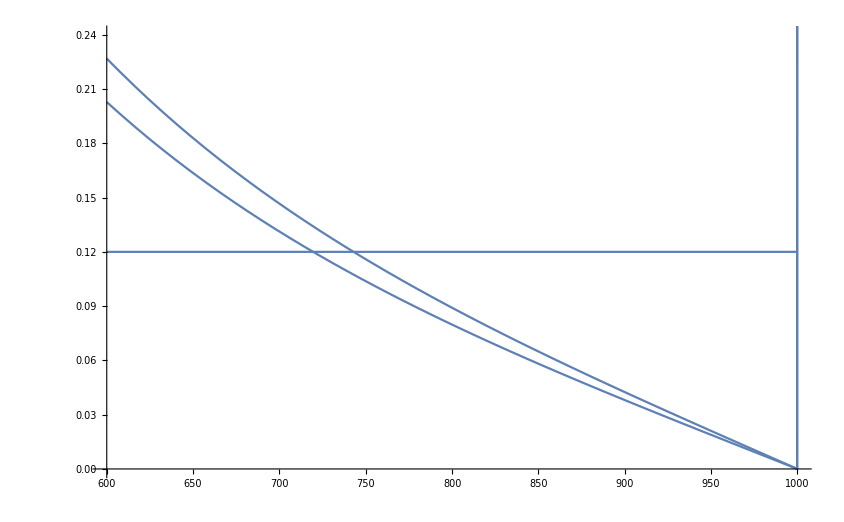

```mathematica
Show[AR,A2,A3]
```

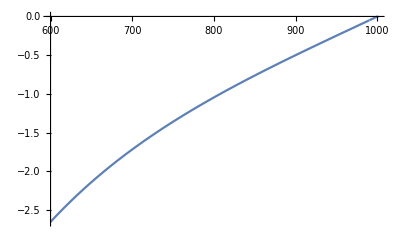

```mathematica
Block[{MV1,MV2,MVC,MZ,sw,cw,Λ},
MV2=990;
MVC=1000;
sw=0.4;
cw=√(1-sw^2);
MZ=91.1;
Λ=1000;
A3=Plot[T30,{MV1,600,1000}]]
```

```mathematica
Clear[T21]
```

```mathematica
T20=T1/.Repμ//Simplify;
T21=Series[T20,{Δ,0,1}];
T22=Normal[T21]/.{Δ->Log[Λ^2/μ^2]};
```

```mathematica
N[Log[100]]
```

4.60517

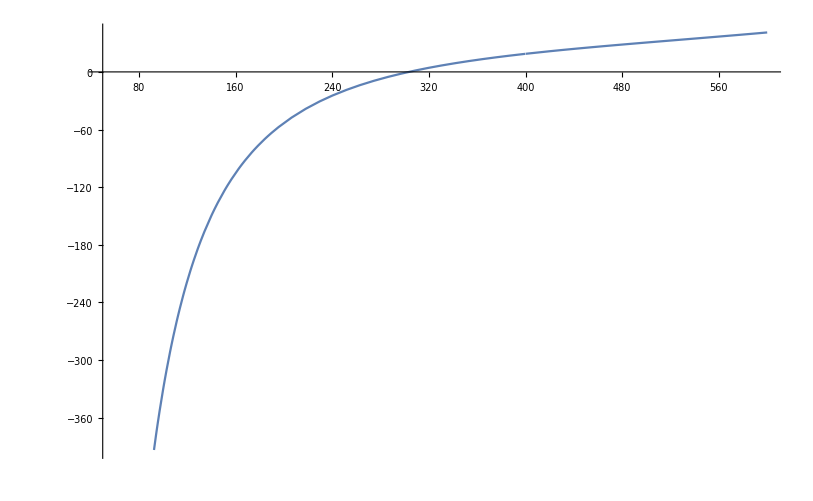

```mathematica
Block[{MV1,MV2,MVC,MZ,sw,cw,Λ,μ},
MV2=400;
MVC=620;
sw=0.4;
cw=√(1-sw^2);
MZ=91.1;
Λ=2000;
μ=MZ;
A3=Plot[T22,{MV1,50,600}]]
```

```mathematica
T22
```

1/(1536 MZ^2 π sw^2)(((-MV1^4+2 MV2^2 log(MV1^2/MV2^2) MV1^2+MV2^4) MV1^6)/(cw^2 MV2^2 (MV2^2-MV1^2)^3)+((MV1^4-2 MVC^2 log(MV1^2/MVC^2) MV1^2-MVC^4) MV1^6)/(cw^2 MVC^2 (MVC^2-MV1^2)^3)+(8 (MV1^4-2 MV2^2 log(MV1^2/MV2^2) MV1^2-MV2^4) MV1^4)/(cw^2 (MV1^2-MV2^2)^3)+(18 (MV1^2 log(MV1^2)-MV2^2 log(MV2^2)) MV1^4)/(cw^2 MV2^2 (MV1^2-MV2^2))+(8 (-MV1^4+2 MVC^2 log(MV1^2/MVC^2) MV1^2+MVC^4) MV1^4)/(cw^2 (MV1^2-MVC^2)^3)+(18 (-log(MV1^2) MV1^2+MV1^2-MVC^2+MVC^2 log(MVC^2)) MV1^4)/(cw^2 MVC^2 (MV1^2-MVC^2))-(14 MV1^4)/(cw^2 MV2^2)-(4 MV1^4)/(cw^2 MVC^2)-(18 MV2^2 (MV1^4-2 MV2^2 log(MV1^2/MV2^2) MV1^2-MV2^4) MV1^2)/(cw^2 (MV1^2-MV2^2)^3)-(20 (μ^2-log(MV2^2)) MV1^2)/(cw^2 μ^2)-(86 (MV1^2 log(MV1^2)-MV2^2 log(MV2^2)) MV1^2)/(cw^2 (MV1^2-MV2^2))+(18 MVC^2 (MV1^4-2 MVC^2 log(MV1^2/MVC^2) MV1^2-MVC^4) MV1^2)/(cw^2 (MV1^2-MVC^2)^3)+(20 (μ^2-log(MVC^2)) MV1^2)/(cw^2 μ^2)-(86 (-log(MV1^2) MV1^2+MV1^2-MVC^2+MVC^2 log(MVC^2)) MV1^2)/(cw^2 (MV1^2-MVC^2))+(86 MV1^2)/cw^2-(4 MVC^4)/(cw^2 MV2^2)+(50 MV2^2)/cw^2+(8 MVC^2)/cw^2+(8 MV2^4 (-MV1^4+2 MV2^2 log(MV1^2/MV2^2) MV1^2+MV2^4))/(cw^2 (MV2^2-MV1^2)^3)+(40 MV2^2 (μ^2-log(MV2^2)))/(cw^2 μ^2)+(24 MVC^2 (μ^2-log(MV2^2)))/(cw^2 μ^2)+(50 MV2^2 (MV2^2 log(MV2^2)-MV1^2 log(MV1^2)))/(cw^2 (MV1^2-MV2^2))+(8 MVC^4 (-MV1^4+2 MVC^2 log(MV1^2/MVC^2) MV1^2+MVC^4))/(cw^2 (MV1^2-MVC^2)^3)+(18 MV2^2 MVC^2 (MV2^4-2 MVC^2 log(MV2^2/MVC^2) MV2^2-MVC^4))/(cw^2 (MV2^2-MVC^2)^3)+(MV2^6 (MV2^4-2 MVC^2 log(MV2^2/MVC^2) MV2^2-MVC^4))/(cw^2 MVC^2 (MVC^2-MV2^2)^3)+(MVC^6 (-MV2^4+2 MVC^2 log(MV2^2/MVC^2) MV2^2+MVC^4))/(cw^2 MV2^2 (MV2^2-MVC^2)^3)+(8 MV2^4 (-MV2^4+2 MVC^2 log(MV2^2/MVC^2) MV2^2+MVC^4))/(cw^2 (MV2^2-MVC^2)^3)+(8 MVC^4 (-MV2^4+2 MVC^2 log(MV2^2/MVC^2) MV2^2+MVC^4))/(cw^2 (MV2^2-MVC^2)^3)-(4 MVC^4 (μ^2-log(MVC^2)))/(cw^2 MV2^2 μ^2)+(20 MV2^2 (μ^2-log(MVC^2)))/(cw^2 μ^2)-(80 MVC^2 (μ^2-log(MVC^2)))/(cw^2 μ^2)+(384 cw^2 MVC^2 log(MVC^2))/μ^2-(384 MVC^2 log(MVC^2))/μ^2-(50 MVC^2 (-log(MV1^2) MV1^2+MV1^2-MVC^2+MVC^2 log(MVC^2)))/(cw^2 (MV1^2-MVC^2))+(22 MVC^4 (-log(MV2^2) MV2^2+MV2^2-MVC^2+MVC^2 log(MVC^2)))/(cw^2 MV2^2 (MV2^2-MVC^2))-(86 MV2^2 (-log(MV2^2) MV2^2+MV2^2-MVC^2+MVC^2 log(MVC^2)))/(cw^2 (MV2^2-MVC^2))-(50 MVC^2 (-log(MV2^2) MV2^2+MV2^2-MVC^2+MVC^2 log(MVC^2)))/(cw^2 (MV2^2-MVC^2))+(18 MV2^4 (-log(MV2^2) MV2^2+MV2^2-MVC^2+MVC^2 log(MVC^2)))/(cw^2 MVC^2 (MV2^2-MVC^2))+(24 (MV2^2 log(MV1^2/μ^2)-MV2^2))/cw^2-(24 (MVC^2 log(MV1^2/μ^2)-MVC^2))/cw^2-384 cw^2 MVC^2 log(MVC^2/μ^2)-(96 MVC^2 log(MVC^2/μ^2))/cw^2+384 MVC^2 log(MVC^2/μ^2)-(4 MV2^4)/(cw^2 MVC^2)-(18 MV2^4)/(cw^2 MV1^2)-(4 MVC^4)/(cw^2 MV1^2)+(MV2^6 (MV1^4-2 MV2^2 log(MV1^2/MV2^2) MV1^2-MV2^4))/(cw^2 (MV1^2-MV2^2)^3 MV1^2)+(4 MV2^4 (μ^2-log(MV2^2)))/(cw^2 μ^2 MV1^2)+(22 MV2^4 (MV1^2 log(MV1^2)-MV2^2 log(MV2^2)))/(cw^2 (MV1^2-MV2^2) MV1^2)+(MVC^6 (-MV1^4+2 MVC^2 log(MV1^2/MVC^2) MV1^2+MVC^4))/(cw^2 (MV1^2-MVC^2)^3 MV1^2)-(4 MVC^4 (μ^2-log(MVC^2)))/(cw^2 μ^2 MV1^2)+(22 MVC^4 (-log(MV1^2) MV1^2+MV1^2-MVC^2+MVC^2 log(MVC^2)))/(cw^2 (MV1^2-MVC^2) MV1^2))+(3 (MV2^2 MV1^6-MVC^2 MV1^6+MV2^6 MV1^2+MVC^6 MV1^2-2 MV2^2 MVC^4 MV1^2+MV2^2 MVC^6-MV2^6 MVC^2) log(Λ^2/μ^2))/(256 cw^2 MV1^2 MV2^2 MVC^2 MZ^2 π sw^2)

Another DB0 replacement

```mathematica
(*Quizá esto no está bien*)
```

```mathematica
Rep1:={
DB0[0,MV1^2,MV2^2]->4*B0[0,MV1^2,MV2^2]-2,
DB0[0,MV1^2,MVC^2]->4*B0[0,MV1^2,MVC^2]-2,
DB0[0,MV2^2,MVC^2]->4*B0[0,MV2^2,MVC^2]-2
};
Rep2:={
A0[MV1^2]->(MV1^2)(Δ+1-Log[MV1^2]),
A0[MV2^2]->(MV2^2)(Δ+1-Log[MV2^2]),
A0[MVC^2]->(MVC^2)(Δ+1-Log[MVC^2]),
B0[0,MV1^2,MV2^2]->Δ+1-(MV1^2Log[MV1^2]-MV2^2Log[MV2^2])/(MV1^2-MV2^2),
B0[0,MV1^2,MVC^2]->Δ+1-(MV1^2Log[MV1^2]-MVC^2Log[MVC^2])/(MV1^2-MVC^2),
B0[0,MV2^2,MVC^2]->Δ+1-(MV2^2Log[MV2^2]-MVC^2Log[MVC^2])/(MV2^2-MVC^2),
B0[0,MV1^2,MV1^2]->Δ-Log[MV1^2],
B0[0,MV2^2,MV2^2]->Δ-Log[MV2^2],
B0[0,MVC^2,MVC^2]->Δ-Log[MVC^2]
};
```

```mathematica
T4=T1/.Rep1//Simplify;
T5=T4/.Rep2//Simplify;
```

```mathematica
Series[T5,{Δ,0,1}]//Simplify;
```

T-parameter (non-simple form)

```mathematica
T9=Simplify[WW0/(cw*MZ)^2-ZZ0/MZ^2-2*sw/cw ZγMZ/MZ^2]/α/.{α->e^2/(4π)};
T10=T9/.Rep//Simplify;
T11=Series[T10,{Δ,0,0}]//Simplify;
```

```mathematica
T12=Simplify[Numerator[Normal[T11]]];
```

```mathematica
T12/.{MV2->MVC}
```

Power::infy: Infinite expression 1/0^3 encountered.

Infinity::indet: Indeterminate expression 0 MV1^2 MVC^8 ComplexInfinity
 encountered.

Power::infy: Infinite expression 1/0^3 encountered.

Infinity::indet: Indeterminate expression 0 MV1^2 MVC^8 ComplexInfinity
 encountered.

Power::infy: Infinite expression 1/0^3 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 MV1^2 MVC^2 MVC^6 ComplexInfinity
 encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Indeterminate

## Trush

```mathematica
SetOptions[{B0,B1,B00,B11},BReduce->True]
```

SetOptions::sstm: Argument B0i(bb0,##1)& is not a symbol or a stream.

SetOptions[{B0i(bb0,##1)&,B1,B00,B11},BReduce→True]

```mathematica
AA=Series[B0[x,MV1^2,MV2^2],{x,0,1}]
```

B_0(0,MV1^2,MV2^2)+x DB0(0,MV1^2,MV2^2)+O(x^2)

```mathematica
7
```

```mathematica
AO[MVC^2]->MVC^2*(B0[0,MVC^2,MVC^2]-1)
```

```mathematica
f[m0_,m1_]:=-∫_0^1 (x*(1-x))/(x*m1^2+(1-x)*m0^2)ⅆx
```

```mathematica
-∫_0^1 (x*(1-x))/(x*m1^2+(1-x)*m0^2)ⅆx
```

ConditionalExpression[-(m0^4+2 m0^2 m1^2 (log(-m1^2)-log(-m0^2))-m1^4)/(2 (m0^2-m1^2)^3),Re(m0^2/(m0^2-m1^2))>1∨Re(m0^2/(m0^2-m1^2))<0∨m0^2/(m0^2-m1^2)∉ℝ]

```mathematica
f[2,10]
```

(25 log(5)-156)/27648

```mathematica
f[10,2]
```

(25 log(5)-156)/27648

```mathematica
DB0[0,MV1^2,MV2^2]->-(MV1^4-2 MV2^2 Log[-MV1^2] MV1^2+2 MV2^2 Log[-MV2^2] MV1^2-MV2^4)/(2 (MV1^2-MV2^2)^3),
DB0[0,MV1^2,MVC^2]->-(MV1^4-2 MVC^2 Log[-MV1^2] MV1^2+2 MVC^2 Log[-MVC^2] MV1^2-MVC^4)/(2 (MV1^2-MVC^2)^3),
DB0[0,MV2^2,MVC^2]->-(MV2^4-2 MVC^2 Log[-MV2^2] MV2^2+2 MVC^2 Log[-MVC^2] MV2^2-MVC^4)/(2 (MV2^2-MVC^2)^3)
```

```mathematica
Block[{m0,m1},Assuming[m0∈ Real&& m1∈ Real,
-∫_0^1 (x*(1-x))/(x*m1^2+(1-x)*m0^2)ⅆx]]
```

Element::bset: The second argument Real of Element should be one of: Primes, Integers, Rationals, Algebraics, Reals, Complexes, or Booleans.

ConditionalExpression[-(m0^4+2 m0^2 m1^2 (log(-m1^2)-log(-m0^2))-m1^4)/(2 (m0^2-m1^2)^3),(Im(m0))^2≥(Re(m0))^2∧(Im(m1))^2≥(Re(m1))^2∧(Re(m0^2/(m0^2-m1^2))<0∨Re(m0^2/(m0^2-m1^2))>1∨m0^2/(m0^2-m1^2)∉ℝ)]

```mathematica
Block[{m0,m1},m0>0;m1>0&&m1>m0&&Im[m1]=0&&Im[m0];
-∫_0^1 (x*(1-x))/(x*m1^2+(1-x)*m0^2)ⅆx]
ConditionalExpression[-(m0^4-2 m1^2 log(-m0^2) m0^2+2 m1^2 log(-m1^2) m0^2-m1^4)/(2 (m0^2-m1^2)^3),((Im(m0)<0∧((Re(m0)<0∧((Im(m1)<0∧Re(m1)≤-(Im(m0) Im(m1))/(Re(m0))∧(Re(m0^2/(m0^2-m1^2))<0∨(0≤Re(m0^2/(m0^2-m1^2))≤1∧(Im(m0^2/(m0^2-m1^2))<0∨Im(m0^2/(m0^2-m1^2))>0))∨Re(m0^2/(m0^2-m1^2))>1))∨(m1∈Reals∧(Re(m0^2/(m0^2-m1^2))<0∨(0≤Re(m0^2/(m0^2-m1^2))≤1∧(Im(m0^2/(m0^2-m1^2))<0∨Im(m0^2/(m0^2-m1^2))>0))∨Re(m0^2/(m0^2-m1^2))>1))∨(Im(m1)>0∧Re(m1)≥-(Im(m0) Im(m1))/(Re(m0))∧(Re(m0^2/(m0^2-m1^2))<0∨(0≤Re(m0^2/(m0^2-m1^2))≤1∧(Im(m0^2/(m0^2-m1^2))<0∨Im(m0^2/(m0^2-m1^2))>0))∨Re(m0^2/(m0^2-m1^2))>1))))∨(Re(m0)==0∧(Re(m0^2/(m0^2-m1^2))<0∨(0≤Re(m0^2/(m0^2-m1^2))≤1∧(Im(m0^2/(m0^2-m1^2))<0∨Im(m0^2/(m0^2-m1^2))>0))∨Re(m0^2/(m0^2-m1^2))>1))∨(Re(m0)>0∧((Im(m1)<0∧Re(m1)≥-(Im(m0) Im(m1))/(Re(m0))∧(Re(m0^2/(m0^2-m1^2))<0∨(0≤Re(m0^2/(m0^2-m1^2))≤1∧(Im(m0^2/(m0^2-m1^2))<0∨Im(m0^2/(m0^2-m1^2))>0))∨Re(m0^2/(m0^2-m1^2))>1))∨(m1∈Reals∧(Re(m0^2/(m0^2-m1^2))<0∨(0≤Re(m0^2/(m0^2-m1^2))≤1∧(Im(m0^2/(m0^2-m1^2))<0∨Im(m0^2/(m0^2-m1^2))>0))∨Re(m0^2/(m0^2-m1^2))>1))∨(Im(m1)>0∧Re(m1)≤-(Im(m0) Im(m1))/(Re(m0))∧(Re(m0^2/(m0^2-m1^2))<0∨(0≤Re(m0^2/(m0^2-m1^2))≤1∧(Im(m0^2/(m0^2-m1^2))<0∨Im(m0^2/(m0^2-m1^2))>0))∨Re(m0^2/(m0^2-m1^2))>1))))))∨(m0∈Reals∧(Re(m0^2/(m0^2-m1^2))<0∨(0≤Re(m0^2/(m0^2-m1^2))≤1∧(Im(m0^2/(m0^2-m1^2))<0∨Im(m0^2/(m0^2-m1^2))>0))∨Re(m0^2/(m0^2-m1^2))>1))∨(Im(m0)>0∧((Re(m0)<0∧((Im(m1)<0∧Re(m1)≥-(Im(m0) Im(m1))/(Re(m0))∧(Re(m0^2/(m0^2-m1^2))<0∨(0≤Re(m0^2/(m0^2-m1^2))≤1∧(Im(m0^2/(m0^2-m1^2))<0∨Im(m0^2/(m0^2-m1^2))>0))∨Re(m0^2/(m0^2-m1^2))>1))∨(m1∈Reals∧(Re(m0^2/(m0^2-m1^2))<0∨(0≤Re(m0^2/(m0^2-m1^2))≤1∧(Im(m0^2/(m0^2-m1^2))<0∨Im(m0^2/(m0^2-m1^2))>0))∨Re(m0^2/(m0^2-m1^2))>1))∨(Im(m1)>0∧Re(m1)≤-(Im(m0) Im(m1))/(Re(m0))∧(Re(m0^2/(m0^2-m1^2))<0∨(0≤Re(m0^2/(m0^2-m1^2))≤1∧(Im(m0^2/(m0^2-m1^2))<0∨Im(m0^2/(m0^2-m1^2))>0))∨Re(m0^2/(m0^2-m1^2))>1))))∨(Re(m0)==0∧(Re(m0^2/(m0^2-m1^2))<0∨(0≤Re(m0^2/(m0^2-m1^2))≤1∧(Im(m0^2/(m0^2-m1^2))<0∨Im(m0^2/(m0^2-m1^2))>0))∨Re(m0^2/(m0^2-m1^2))>1))∨(Re(m0)>0∧((Im(m1)<0∧Re(m1)≤-(Im(m0) Im(m1))/(Re(m0))∧(Re(m0^2/(m0^2-m1^2))<0∨(0≤Re(m0^2/(m0^2-m1^2))≤1∧(Im(m0^2/(m0^2-m1^2))<0∨Im(m0^2/(m0^2-m1^2))>0))∨Re(m0^2/(m0^2-m1^2))>1))∨(m1∈Reals∧(Re(m0^2/(m0^2-m1^2))<0∨(0≤Re(m0^2/(m0^2-m1^2))≤1∧(Im(m0^2/(m0^2-m1^2))<0∨Im(m0^2/(m0^2-m1^2))>0))∨Re(m0^2/(m0^2-m1^2))>1))∨(Im(m1)>0∧Re(m1)≥-(Im(m0) Im(m1))/(Re(m0))∧(Re(m0^2/(m0^2-m1^2))<0∨(0≤Re(m0^2/(m0^2-m1^2))≤1∧(Im(m0^2/(m0^2-m1^2))<0∨Im(m0^2/(m0^2-m1^2))>0))∨Re(m0^2/(m0^2-m1^2))>1)))))))∧(Im(m0^2/(m0^2-m1^2))≠0∨Re(m0^2/(m0^2-m1^2))>1∨Re(m0^2/(m0^2-m1^2))<0)∧((Im(m0) Re(m0)≥0∧Re(m0^2/(m0^2-m1^2))≥1∧Im(m0) Re(m0)≤Im(m1) Re(m1))∨(Im(m0) Re(m0)≥0∧Im(m0) Re(m0)≤Im(m1) Re(m1)∧Re(m0^2/(m0^2-m1^2))≤0)∨(Im(m0) Re(m0)≥0∧Im(m0) Re(m0)≤Im(m1) Re(m1)∧Im(m0^2/(m0^2-m1^2))≠0)∨(Im(m0) Re(m0)≥Im(m1) Re(m1)∧Im(m1) Re(m1)≥0∧Re(m0^2/(m0^2-m1^2))≥1)∨(Im(m0) Re(m0)≥Im(m1) Re(m1)∧Im(m1) Re(m1)≥0∧Re(m0^2/(m0^2-m1^2))≤0)∨(Im(m0) Re(m0)≥Im(m1) Re(m1)∧Im(m1) Re(m1)≥0∧Im(m0^2/(m0^2-m1^2))≠0)∨(Im(m0) Re(m0)≥Im(m1) Re(m1)∧(Im(m1) Re(m0)-Im(m0) Re(m1)) (Im(m0) Im(m1)+Re(m0) Re(m1))≥0∧Re(m0^2/(m0^2-m1^2))≥1)∨(Im(m0) Re(m0)≥Im(m1) Re(m1)∧(Im(m1) Re(m0)-Im(m0) Re(m1)) (Im(m0) Im(m1)+Re(m0) Re(m1))≥0∧Re(m0^2/(m0^2-m1^2))≤0)∨(Im(m0) Re(m0)≥Im(m1) Re(m1)∧(Im(m1) Re(m0)-Im(m0) Re(m1)) (Im(m0) Im(m1)+Re(m0) Re(m1))≥0∧Im(m0^2/(m0^2-m1^2))≠0)∨(Im(m0) Re(m0)≥Im(m1) Re(m1)∧Re(m0^2/(m0^2-m1^2))≥1∧Im(m0) Re(m0)≤0)∨(Im(m0) Re(m0)≥Im(m1) Re(m1)∧Im(m0) Re(m0)≤0∧Re(m0^2/(m0^2-m1^2))≤0)∨(Im(m0) Re(m0)≥Im(m1) Re(m1)∧Im(m0) Re(m0)≤0∧Im(m0^2/(m0^2-m1^2))≠0)∨(Re(m0^2/(m0^2-m1^2))≥1∧Im(m0) Re(m0)≤Im(m1) Re(m1)∧Im(m1) Re(m1)≤0)∨(Re(m0^2/(m0^2-m1^2))≥1∧Im(m0) Re(m0)≤Im(m1) Re(m1)∧(Im(m1) Re(m0)-Im(m0) Re(m1)) (Im(m0) Im(m1)+Re(m0) Re(m1))≤0)∨(Im(m0) Re(m0)≤Im(m1) Re(m1)∧Im(m1) Re(m1)≤0∧Re(m0^2/(m0^2-m1^2))≤0)∨(Im(m0) Re(m0)≤Im(m1) Re(m1)∧Im(m1) Re(m1)≤0∧Im(m0^2/(m0^2-m1^2))≠0)∨(Im(m0) Re(m0)≤Im(m1) Re(m1)∧(Im(m1) Re(m0)-Im(m0) Re(m1)) (Im(m0) Im(m1)+Re(m0) Re(m1))≤0∧Re(m0^2/(m0^2-m1^2))≤0)∨(Im(m0) Re(m0)≤Im(m1) Re(m1)∧(Im(m1) Re(m0)-Im(m0) Re(m1)) (Im(m0) Im(m1)+Re(m0) Re(m1))≤0∧Im(m0^2/(m0^2-m1^2))≠0))]
```

ConditionalExpression[-(m0^4-2 m1^2 log(-m0^2) m0^2+2 m1^2 log(-m1^2) m0^2-m1^4)/(2 (m0^2-m1^2)^3),((Im(m0)<0∧((Re(m0)<0∧((Im(m1)<0∧Re(m1)≤-(Im(m0) Im(m1))/(Re(m0))∧(Re(m0^2/(m0^2-m1^2))<0∨(0≤Re(m0^2/(m0^2-m1^2))≤1∧(Im(m0^2/(m0^2-m1^2))<0∨Im(m0^2/(m0^2-m1^2))>0))∨Re(m0^2/(m0^2-m1^2))>1))∨(m1∈ℝ∧(Re(m0^2/(m0^2-m1^2))<0∨(0≤Re(m0^2/(m0^2-m1^2))≤1∧(Im(m0^2/(m0^2-m1^2))<0∨Im(m0^2/(m0^2-m1^2))>0))∨Re(m0^2/(m0^2-m1^2))>1))∨(Im(m1)>0∧Re(m1)≥-(Im(m0) Im(m1))/(Re(m0))∧(Re(m0^2/(m0^2-m1^2))<0∨(0≤Re(m0^2/(m0^2-m1^2))≤1∧(Im(m0^2/(m0^2-m1^2))<0∨Im(m0^2/(m0^2-m1^2))>0))∨Re(m0^2/(m0^2-m1^2))>1))))∨(Re(m0)==0∧(Re(m0^2/(m0^2-m1^2))<0∨(0≤Re(m0^2/(m0^2-m1^2))≤1∧(Im(m0^2/(m0^2-m1^2))<0∨Im(m0^2/(m0^2-m1^2))>0))∨Re(m0^2/(m0^2-m1^2))>1))∨(Re(m0)>0∧((Im(m1)<0∧Re(m1)≥-(Im(m0) Im(m1))/(Re(m0))∧(Re(m0^2/(m0^2-m1^2))<0∨(0≤Re(m0^2/(m0^2-m1^2))≤1∧(Im(m0^2/(m0^2-m1^2))<0∨Im(m0^2/(m0^2-m1^2))>0))∨Re(m0^2/(m0^2-m1^2))>1))∨(m1∈ℝ∧(Re(m0^2/(m0^2-m1^2))<0∨(0≤Re(m0^2/(m0^2-m1^2))≤1∧(Im(m0^2/(m0^2-m1^2))<0∨Im(m0^2/(m0^2-m1^2))>0))∨Re(m0^2/(m0^2-m1^2))>1))∨(Im(m1)>0∧Re(m1)≤-(Im(m0) Im(m1))/(Re(m0))∧(Re(m0^2/(m0^2-m1^2))<0∨(0≤Re(m0^2/(m0^2-m1^2))≤1∧(Im(m0^2/(m0^2-m1^2))<0∨Im(m0^2/(m0^2-m1^2))>0))∨Re(m0^2/(m0^2-m1^2))>1))))))∨(m0∈ℝ∧(Re(m0^2/(m0^2-m1^2))<0∨(0≤Re(m0^2/(m0^2-m1^2))≤1∧(Im(m0^2/(m0^2-m1^2))<0∨Im(m0^2/(m0^2-m1^2))>0))∨Re(m0^2/(m0^2-m1^2))>1))∨(Im(m0)>0∧((Re(m0)<0∧((Im(m1)<0∧Re(m1)≥-(Im(m0) Im(m1))/(Re(m0))∧(Re(m0^2/(m0^2-m1^2))<0∨(0≤Re(m0^2/(m0^2-m1^2))≤1∧(Im(m0^2/(m0^2-m1^2))<0∨Im(m0^2/(m0^2-m1^2))>0))∨Re(m0^2/(m0^2-m1^2))>1))∨(m1∈ℝ∧(Re(m0^2/(m0^2-m1^2))<0∨(0≤Re(m0^2/(m0^2-m1^2))≤1∧(Im(m0^2/(m0^2-m1^2))<0∨Im(m0^2/(m0^2-m1^2))>0))∨Re(m0^2/(m0^2-m1^2))>1))∨(Im(m1)>0∧Re(m1)≤-(Im(m0) Im(m1))/(Re(m0))∧(Re(m0^2/(m0^2-m1^2))<0∨(0≤Re(m0^2/(m0^2-m1^2))≤1∧(Im(m0^2/(m0^2-m1^2))<0∨Im(m0^2/(m0^2-m1^2))>0))∨Re(m0^2/(m0^2-m1^2))>1))))∨(Re(m0)==0∧(Re(m0^2/(m0^2-m1^2))<0∨(0≤Re(m0^2/(m0^2-m1^2))≤1∧(Im(m0^2/(m0^2-m1^2))<0∨Im(m0^2/(m0^2-m1^2))>0))∨Re(m0^2/(m0^2-m1^2))>1))∨(Re(m0)>0∧((Im(m1)<0∧Re(m1)≤-(Im(m0) Im(m1))/(Re(m0))∧(Re(m0^2/(m0^2-m1^2))<0∨(0≤Re(m0^2/(m0^2-m1^2))≤1∧(Im(m0^2/(m0^2-m1^2))<0∨Im(m0^2/(m0^2-m1^2))>0))∨Re(m0^2/(m0^2-m1^2))>1))∨(m1∈ℝ∧(Re(m0^2/(m0^2-m1^2))<0∨(0≤Re(m0^2/(m0^2-m1^2))≤1∧(Im(m0^2/(m0^2-m1^2))<0∨Im(m0^2/(m0^2-m1^2))>0))∨Re(m0^2/(m0^2-m1^2))>1))∨(Im(m1)>0∧Re(m1)≥-(Im(m0) Im(m1))/(Re(m0))∧(Re(m0^2/(m0^2-m1^2))<0∨(0≤Re(m0^2/(m0^2-m1^2))≤1∧(Im(m0^2/(m0^2-m1^2))<0∨Im(m0^2/(m0^2-m1^2))>0))∨Re(m0^2/(m0^2-m1^2))>1)))))))∧(Im(m0^2/(m0^2-m1^2))≠0∨Re(m0^2/(m0^2-m1^2))>1∨Re(m0^2/(m0^2-m1^2))<0)∧((Im(m0) Re(m0)≥0∧Re(m0^2/(m0^2-m1^2))≥1∧Im(m0) Re(m0)≤Im(m1) Re(m1))∨(Im(m0) Re(m0)≥0∧Im(m0) Re(m0)≤Im(m1) Re(m1)∧Re(m0^2/(m0^2-m1^2))≤0)∨(Im(m0) Re(m0)≥0∧Im(m0) Re(m0)≤Im(m1) Re(m1)∧Im(m0^2/(m0^2-m1^2))≠0)∨(Im(m0) Re(m0)≥Im(m1) Re(m1)∧Im(m1) Re(m1)≥0∧Re(m0^2/(m0^2-m1^2))≥1)∨(Im(m0) Re(m0)≥Im(m1) Re(m1)∧Im(m1) Re(m1)≥0∧Re(m0^2/(m0^2-m1^2))≤0)∨(Im(m0) Re(m0)≥Im(m1) Re(m1)∧Im(m1) Re(m1)≥0∧Im(m0^2/(m0^2-m1^2))≠0)∨(Im(m0) Re(m0)≥Im(m1) Re(m1)∧(Im(m1) Re(m0)-Im(m0) Re(m1)) (Im(m0) Im(m1)+Re(m0) Re(m1))≥0∧Re(m0^2/(m0^2-m1^2))≥1)∨(Im(m0) Re(m0)≥Im(m1) Re(m1)∧(Im(m1) Re(m0)-Im(m0) Re(m1)) (Im(m0) Im(m1)+Re(m0) Re(m1))≥0∧Re(m0^2/(m0^2-m1^2))≤0)∨(Im(m0) Re(m0)≥Im(m1) Re(m1)∧(Im(m1) Re(m0)-Im(m0) Re(m1)) (Im(m0) Im(m1)+Re(m0) Re(m1))≥0∧Im(m0^2/(m0^2-m1^2))≠0)∨(Im(m0) Re(m0)≥Im(m1) Re(m1)∧Re(m0^2/(m0^2-m1^2))≥1∧Im(m0) Re(m0)≤0)∨(Im(m0) Re(m0)≥Im(m1) Re(m1)∧Im(m0) Re(m0)≤0∧Re(m0^2/(m0^2-m1^2))≤0)∨(Im(m0) Re(m0)≥Im(m1) Re(m1)∧Im(m0) Re(m0)≤0∧Im(m0^2/(m0^2-m1^2))≠0)∨(Re(m0^2/(m0^2-m1^2))≥1∧Im(m0) Re(m0)≤Im(m1) Re(m1)∧Im(m1) Re(m1)≤0)∨(Re(m0^2/(m0^2-m1^2))≥1∧Im(m0) Re(m0)≤Im(m1) Re(m1)∧(Im(m1) Re(m0)-Im(m0) Re(m1)) (Im(m0) Im(m1)+Re(m0) Re(m1))≤0)∨(Im(m0) Re(m0)≤Im(m1) Re(m1)∧Im(m1) Re(m1)≤0∧Re(m0^2/(m0^2-m1^2))≤0)∨(Im(m0) Re(m0)≤Im(m1) Re(m1)∧Im(m1) Re(m1)≤0∧Im(m0^2/(m0^2-m1^2))≠0)∨(Im(m0) Re(m0)≤Im(m1) Re(m1)∧(Im(m1) Re(m0)-Im(m0) Re(m1)) (Im(m0) Im(m1)+Re(m0) Re(m1))≤0∧Re(m0^2/(m0^2-m1^2))≤0)∨(Im(m0) Re(m0)≤Im(m1) Re(m1)∧(Im(m1) Re(m0)-Im(m0) Re(m1)) (Im(m0) Im(m1)+Re(m0) Re(m1))≤0∧Im(m0^2/(m0^2-m1^2))≠0))]

ConditionalExpression[-(m0^4-2 m1^2 log(-m0^2) m0^2+2 m1^2 log(-m1^2) m0^2-m1^4)/(2 (m0^2-m1^2)^3),((Im(m0)<0∧((Re(m0)<0∧((Im(m1)<0∧Re(m1)≤-(Im(m0) Im(m1))/(Re(m0))∧(Re(m0^2/(m0^2-m1^2))<0∨(0≤Re(m0^2/(m0^2-m1^2))≤1∧(Im(m0^2/(m0^2-m1^2))<0∨Im(m0^2/(m0^2-m1^2))>0))∨Re(m0^2/(m0^2-m1^2))>1))∨(m1∈ℝ∧(Re(m0^2/(m0^2-m1^2))<0∨(0≤Re(m0^2/(m0^2-m1^2))≤1∧(Im(m0^2/(m0^2-m1^2))<0∨Im(m0^2/(m0^2-m1^2))>0))∨Re(m0^2/(m0^2-m1^2))>1))∨(Im(m1)>0∧Re(m1)≥-(Im(m0) Im(m1))/(Re(m0))∧(Re(m0^2/(m0^2-m1^2))<0∨(0≤Re(m0^2/(m0^2-m1^2))≤1∧(Im(m0^2/(m0^2-m1^2))<0∨Im(m0^2/(m0^2-m1^2))>0))∨Re(m0^2/(m0^2-m1^2))>1))))∨(Re(m0)==0∧(Re(m0^2/(m0^2-m1^2))<0∨(0≤Re(m0^2/(m0^2-m1^2))≤1∧(Im(m0^2/(m0^2-m1^2))<0∨Im(m0^2/(m0^2-m1^2))>0))∨Re(m0^2/(m0^2-m1^2))>1))∨(Re(m0)>0∧((Im(m1)<0∧Re(m1)≥-(Im(m0) Im(m1))/(Re(m0))∧(Re(m0^2/(m0^2-m1^2))<0∨(0≤Re(m0^2/(m0^2-m1^2))≤1∧(Im(m0^2/(m0^2-m1^2))<0∨Im(m0^2/(m0^2-m1^2))>0))∨Re(m0^2/(m0^2-m1^2))>1))∨(m1∈ℝ∧(Re(m0^2/(m0^2-m1^2))<0∨(0≤Re(m0^2/(m0^2-m1^2))≤1∧(Im(m0^2/(m0^2-m1^2))<0∨Im(m0^2/(m0^2-m1^2))>0))∨Re(m0^2/(m0^2-m1^2))>1))∨(Im(m1)>0∧Re(m1)≤-(Im(m0) Im(m1))/(Re(m0))∧(Re(m0^2/(m0^2-m1^2))<0∨(0≤Re(m0^2/(m0^2-m1^2))≤1∧(Im(m0^2/(m0^2-m1^2))<0∨Im(m0^2/(m0^2-m1^2))>0))∨Re(m0^2/(m0^2-m1^2))>1))))))∨(m0∈ℝ∧(Re(m0^2/(m0^2-m1^2))<0∨(0≤Re(m0^2/(m0^2-m1^2))≤1∧(Im(m0^2/(m0^2-m1^2))<0∨Im(m0^2/(m0^2-m1^2))>0))∨Re(m0^2/(m0^2-m1^2))>1))∨(Im(m0)>0∧((Re(m0)<0∧((Im(m1)<0∧Re(m1)≥-(Im(m0) Im(m1))/(Re(m0))∧(Re(m0^2/(m0^2-m1^2))<0∨(0≤Re(m0^2/(m0^2-m1^2))≤1∧(Im(m0^2/(m0^2-m1^2))<0∨Im(m0^2/(m0^2-m1^2))>0))∨Re(m0^2/(m0^2-m1^2))>1))∨(m1∈ℝ∧(Re(m0^2/(m0^2-m1^2))<0∨(0≤Re(m0^2/(m0^2-m1^2))≤1∧(Im(m0^2/(m0^2-m1^2))<0∨Im(m0^2/(m0^2-m1^2))>0))∨Re(m0^2/(m0^2-m1^2))>1))∨(Im(m1)>0∧Re(m1)≤-(Im(m0) Im(m1))/(Re(m0))∧(Re(m0^2/(m0^2-m1^2))<0∨(0≤Re(m0^2/(m0^2-m1^2))≤1∧(Im(m0^2/(m0^2-m1^2))<0∨Im(m0^2/(m0^2-m1^2))>0))∨Re(m0^2/(m0^2-m1^2))>1))))∨(Re(m0)==0∧(Re(m0^2/(m0^2-m1^2))<0∨(0≤Re(m0^2/(m0^2-m1^2))≤1∧(Im(m0^2/(m0^2-m1^2))<0∨Im(m0^2/(m0^2-m1^2))>0))∨Re(m0^2/(m0^2-m1^2))>1))∨(Re(m0)>0∧((Im(m1)<0∧Re(m1)≤-(Im(m0) Im(m1))/(Re(m0))∧(Re(m0^2/(m0^2-m1^2))<0∨(0≤Re(m0^2/(m0^2-m1^2))≤1∧(Im(m0^2/(m0^2-m1^2))<0∨Im(m0^2/(m0^2-m1^2))>0))∨Re(m0^2/(m0^2-m1^2))>1))∨(m1∈ℝ∧(Re(m0^2/(m0^2-m1^2))<0∨(0≤Re(m0^2/(m0^2-m1^2))≤1∧(Im(m0^2/(m0^2-m1^2))<0∨Im(m0^2/(m0^2-m1^2))>0))∨Re(m0^2/(m0^2-m1^2))>1))∨(Im(m1)>0∧Re(m1)≥-(Im(m0) Im(m1))/(Re(m0))∧(Re(m0^2/(m0^2-m1^2))<0∨(0≤Re(m0^2/(m0^2-m1^2))≤1∧(Im(m0^2/(m0^2-m1^2))<0∨Im(m0^2/(m0^2-m1^2))>0))∨Re(m0^2/(m0^2-m1^2))>1)))))))∧(Im(m0^2/(m0^2-m1^2))≠0∨Re(m0^2/(m0^2-m1^2))>1∨Re(m0^2/(m0^2-m1^2))<0)∧((Im(m0) Re(m0)≥0∧Re(m0^2/(m0^2-m1^2))≥1∧Im(m0) Re(m0)≤Im(m1) Re(m1))∨(Im(m0) Re(m0)≥0∧Im(m0) Re(m0)≤Im(m1) Re(m1)∧Re(m0^2/(m0^2-m1^2))≤0)∨(Im(m0) Re(m0)≥0∧Im(m0) Re(m0)≤Im(m1) Re(m1)∧Im(m0^2/(m0^2-m1^2))≠0)∨(Im(m0) Re(m0)≥Im(m1) Re(m1)∧Im(m1) Re(m1)≥0∧Re(m0^2/(m0^2-m1^2))≥1)∨(Im(m0) Re(m0)≥Im(m1) Re(m1)∧Im(m1) Re(m1)≥0∧Re(m0^2/(m0^2-m1^2))≤0)∨(Im(m0) Re(m0)≥Im(m1) Re(m1)∧Im(m1) Re(m1)≥0∧Im(m0^2/(m0^2-m1^2))≠0)∨(Im(m0) Re(m0)≥Im(m1) Re(m1)∧(Im(m1) Re(m0)-Im(m0) Re(m1)) (Im(m0) Im(m1)+Re(m0) Re(m1))≥0∧Re(m0^2/(m0^2-m1^2))≥1)∨(Im(m0) Re(m0)≥Im(m1) Re(m1)∧(Im(m1) Re(m0)-Im(m0) Re(m1)) (Im(m0) Im(m1)+Re(m0) Re(m1))≥0∧Re(m0^2/(m0^2-m1^2))≤0)∨(Im(m0) Re(m0)≥Im(m1) Re(m1)∧(Im(m1) Re(m0)-Im(m0) Re(m1)) (Im(m0) Im(m1)+Re(m0) Re(m1))≥0∧Im(m0^2/(m0^2-m1^2))≠0)∨(Im(m0) Re(m0)≥Im(m1) Re(m1)∧Re(m0^2/(m0^2-m1^2))≥1∧Im(m0) Re(m0)≤0)∨(Im(m0) Re(m0)≥Im(m1) Re(m1)∧Im(m0) Re(m0)≤0∧Re(m0^2/(m0^2-m1^2))≤0)∨(Im(m0) Re(m0)≥Im(m1) Re(m1)∧Im(m0) Re(m0)≤0∧Im(m0^2/(m0^2-m1^2))≠0)∨(Re(m0^2/(m0^2-m1^2))≥1∧Im(m0) Re(m0)≤Im(m1) Re(m1)∧Im(m1) Re(m1)≤0)∨(Re(m0^2/(m0^2-m1^2))≥1∧Im(m0) Re(m0)≤Im(m1) Re(m1)∧(Im(m1) Re(m0)-Im(m0) Re(m1)) (Im(m0) Im(m1)+Re(m0) Re(m1))≤0)∨(Im(m0) Re(m0)≤Im(m1) Re(m1)∧Im(m1) Re(m1)≤0∧Re(m0^2/(m0^2-m1^2))≤0)∨(Im(m0) Re(m0)≤Im(m1) Re(m1)∧Im(m1) Re(m1)≤0∧Im(m0^2/(m0^2-m1^2))≠0)∨(Im(m0) Re(m0)≤Im(m1) Re(m1)∧(Im(m1) Re(m0)-Im(m0) Re(m1)) (Im(m0) Im(m1)+Re(m0) Re(m1))≤0∧Re(m0^2/(m0^2-m1^2))≤0)∨(Im(m0) Re(m0)≤Im(m1) Re(m1)∧(Im(m1) Re(m0)-Im(m0) Re(m1)) (Im(m0) Im(m1)+Re(m0) Re(m1))≤0∧Im(m0^2/(m0^2-m1^2))≠0))]

Pauli-Villars

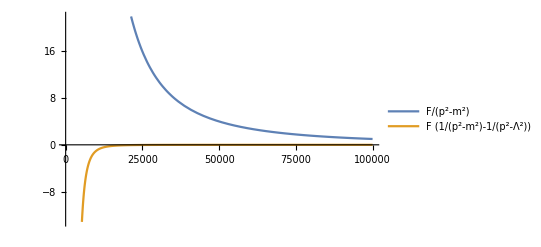

```mathematica
Block[{m,Λ,F},F=10^10;m=1;Λ=10^3;
Plot[{F*(1/(p^2-m^2)),F*(1/(p^2-m^2)-1/(p^2-Λ^2))},{p,0,10^5},PlotLegends->"Expressions"]]
```